```mathematica
tetrahedron := Range[1, 4]
```

```mathematica
cube := Range[1, 6]
```

```mathematica
octahedron := Range[1, 8]
```

```mathematica
dodehedron := Range[1, 12]
```

```mathematica
icosahedron := Range[1, 20]
```

```mathematica
combinations = Tuples[{tetrahedron, cube, octahedron, dodehedron, icosahedron}]
```

{{1,1,1,1,1},{1,1,1,1,2},{1,1,1,1,3},{1,1,1,1,4},{1,1,1,1,5},{1,1,1,1,6},{1,1,1,1,7},{1,1,1,1,8},{1,1,1,1,9},{1,1,1,1,10},{1,1,1,1,11},{1,1,1,1,12},46057,{4,6,8,12,10},{4,6,8,12,11},{4,6,8,12,12},{4,6,8,12,13},{4,6,8,12,14},{4,6,8,12,15},{4,6,8,12,16},{4,6,8,12,17},{4,6,8,12,18},{4,6,8,12,19},{4,6,8,12,20}}
 |  |  |  |

Tuples::normal: Nonatomic expression expected at position {1,1} in Tuples[{tetrahedron,cube,octahedron,dodehedron,icosahedron}].

Tuples[{tetrahedron,cube,octahedron,dodehedron,icosahedron}]

```mathematica
Length[combinations] == 4 * 6 * 8 * 12 * 20
```

True

```mathematica
amounts[H_] := Select[combinations, Function[u, Total[u]==H]]
```

```mathematica
pf[X_]:=Length[amounts[X]]/Length[combinations]
```

```mathematica
pf[5]
```

1/46080

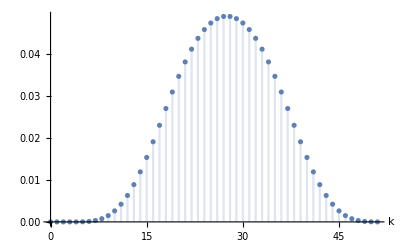

```mathematica
DiscretePlot[pf[k],{k,0,51},AxesLabel->Automatic]
```

```mathematica
Sum[pf[x],{x, 5, 50}]
```

1